```mathematica
σ[z_]:=1/(1+ⅇ^-z)
```

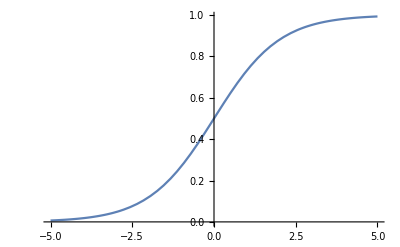

```mathematica
Plot[σ[z],{z, -5, 5}]
```

```mathematica
Dt[σ[z],z]==σ[z](1-σ[z])//TraditionalForm
Simplify[%]
```

ⅇ^-z/((ⅇ^-z+1)^2)==(1-1/(ⅇ^-z+1))/(ⅇ^-z+1)

True

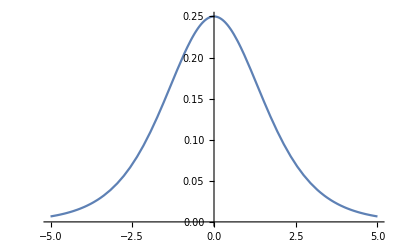

```mathematica
Plot[Evaluate[Dt[σ[z],z]],{z,-5,5}]
```

1/(1+ⅇ^-z)

1/2 (1/(1+ⅇ^-z)-t)^2

-(ⅇ^z (ⅇ^z (-1+t)+t))/((1+ⅇ^z)^3)

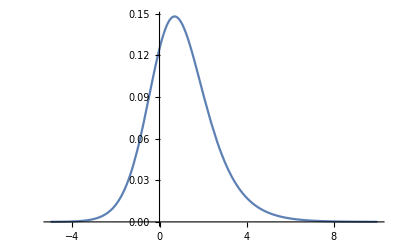

```mathematica
y=σ[z]
err=1/2(y-t)^2
Simplify[Dt[err,z,Constants->t]]
Plot[%/.t->0,{z,-5,10}]
```